```mathematica
nullGenerators4=Table[ChangePrefix[First[Flatten[Values[BaseGenerators2[allGraphs4[k,"colofour"]]]]]],{k,allGraphs4AtomKeys}]
```

{q1x2x3x4,q1x2x34,q1x24x3,q1x23x4,q1x234,q14x2x3,q14x23,q13x2x4,q13x24,q134x2,q12x3x4,q12x34,q124x3,q123x4,q1234}

```mathematica
Table[allGraphs4[k,"colofour"],{k,allGraphs4NullAtomKeys}]
```

```mathematica
nullToGen4=Map[Table[Coefficient[#[[2]],v],{v,nullGenerators4}]&,First[Solve[Fold[And,Table[ChangePrefix[First[Flatten[Values[BaseGenerators2[allGraphs4[k,"colofour"]]]]]]==allGraphs4[k,"colofourrealnull"],{k,allGraphs4GeneratorAtomKeys}]],Table[allGraphs4[k,"colofourrealnull"],{k,allGraphs4NullAtomKeys}]]]];MatrixForm[nullToGen4 ]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
-2 | 1 | 1 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 1
-4 | 2 | 2 | 1 | -1 | 2 | -1 | 1 | -1 | -1 | 1 | -1 | -1 | 0 | 1
-6 | 2 | 2 | 2 | -1 | 2 | -1 | 2 | -1 | -1 | 2 | -1 | -1 | -1 | 1
-4 | 2 | 1 | 2 | -1 | 1 | -1 | 2 | -1 | -1 | 1 | -1 | 0 | -1 | 1
-5 | 1 | 2 | 2 | -1 | 2 | -1 | 2 | -1 | -1 | 1 | 0 | -1 | -1 | 1
-2 | 1 | 1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 1 | -1 | -1 | 0 | 1
-4 | 1 | 2 | 2 | -1 | 1 | -1 | 1 | -1 | 0 | 2 | -1 | -1 | -1 | 1
-5 | 2 | 1 | 2 | -1 | 2 | -1 | 1 | 0 | -1 | 2 | -1 | -1 | -1 | 1
-2 | 1 | 1 | 1 | -1 | 0 | 0 | 1 | -1 | 0 | 1 | -1 | 0 | -1 | 1
-5 | 2 | 2 | 1 | -1 | 1 | 0 | 2 | -1 | -1 | 2 | -1 | -1 | -1 | 1
-2 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | -1 | -1 | 1 | -1 | -1 | 0 | 1
-4 | 1 | 1 | 1 | 0 | 2 | -1 | 2 | -1 | -1 | 2 | -1 | -1 | -1 | 1
-2 | 1 | 0 | 1 | 0 | 1 | -1 | 1 | 0 | -1 | 1 | -1 | 0 | -1 | 1
-2 | 0 | 1 | 1 | 0 | 1 | -1 | 1 | -1 | 0 | 1 | 0 | -1 | -1 | 1)

```mathematica
MatrixForm[Inverse[nullToGen4]]
```

(1 | -1 | 2 | -6 | 2 | 1 | -1 | 2 | 1 | -1 | 1 | -1 | 2 | -1 | -1
1 | -1 | 2 | -4 | 2 | 0 | -1 | 1 | 1 | -1 | 1 | -1 | 1 | -1 | 0
1 | -1 | 2 | -4 | 1 | 1 | -1 | 2 | 0 | -1 | 1 | -1 | 1 | 0 | -1
1 | -1 | 1 | -4 | 2 | 1 | -1 | 2 | 1 | -1 | 0 | 0 | 1 | -1 | -1
1 | -1 | 1 | -1 | 1 | 0 | -1 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0
1 | -1 | 2 | -4 | 1 | 1 | -1 | 1 | 1 | 0 | 0 | -1 | 2 | -1 | -1
1 | -1 | 1 | -3 | 1 | 1 | -1 | 1 | 1 | 0 | 0 | 0 | 1 | -1 | -1
1 | -1 | 1 | -4 | 2 | 1 | 0 | 1 | 0 | -1 | 1 | -1 | 2 | -1 | -1
1 | -1 | 1 | -3 | 1 | 1 | 0 | 1 | 0 | -1 | 1 | -1 | 1 | 0 | -1
1 | -1 | 1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | -1 | 0
1 | 0 | 1 | -4 | 1 | 0 | -1 | 2 | 1 | -1 | 1 | -1 | 2 | -1 | -1
1 | 0 | 1 | -3 | 1 | 0 | -1 | 1 | 1 | -1 | 1 | -1 | 1 | -1 | 0
1 | 0 | 1 | -1 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | -1 | 1 | 0 | -1
1 | 0 | 0 | -1 | 1 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 1 | -1 | -1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Det[Inverse[nullToGen4]]
```

1

```mathematica
fullToGen4=Map[Table[Coefficient[#[[2]],v],{v,nullGenerators4}]&,First[Solve[Fold[And,Table[ChangePrefix[First[Flatten[Values[BaseGenerators2[allGraphs4[k,"colofour"]]]]]]==allGraphs4[k,"colofour"],{k,allGraphs4GeneratorAtomKeys}]],Table[allGraphs4[k,"colofour"],{k,allGraphs4AtomKeys}]]]];MatrixForm[fullToGen4 ]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -1 | -1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | -1 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
2 | -1 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0
2 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0
2 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 1 | 0
-6 | 2 | 2 | 2 | -1 | 2 | -1 | 2 | -1 | -1 | 2 | -1 | -1 | -1 | 1)

```mathematica
MatrixForm[Inverse[fullToGen4 ]]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1)

```mathematica
Total[Flatten[Inverse[fullToGen4 ]]]
```

60

```mathematica
mob4=MobiusMatrix[allGraphs4]
```

{{1,-1,-1,-1,-1,-1,-1,1,1,1,2,2,2,2,-6},{0,1,0,0,0,0,0,-1,0,0,-1,0,0,-1,2},{0,0,1,0,0,0,0,0,0,-1,-1,-1,0,0,2},{0,0,0,1,0,0,0,0,-1,0,-1,0,-1,0,2},{0,0,0,0,1,0,0,-1,0,0,0,-1,-1,0,2},{0,0,0,0,0,1,0,0,-1,0,0,-1,0,-1,2},{0,0,0,0,0,0,1,0,0,-1,0,0,-1,-1,2},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,-1},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,-1},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,-1},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,-1},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,-1},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
zet4=Inverse[mob4]
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,1,0,0,0,0,0,1,0,0,1,0,0,1,1},{0,0,1,0,0,0,0,0,0,1,1,1,0,0,1},{0,0,0,1,0,0,0,0,1,0,1,0,1,0,1},{0,0,0,0,1,0,0,1,0,0,0,1,1,0,1},{0,0,0,0,0,1,0,0,1,0,0,1,0,1,1},{0,0,0,0,0,0,1,0,0,1,0,0,1,1,1},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
Total[Flatten[zet4]]
```

60

```mathematica
{MatrixPlot[Inverse[fullToGen4 ]],MatrixPlot[zet4]}
```

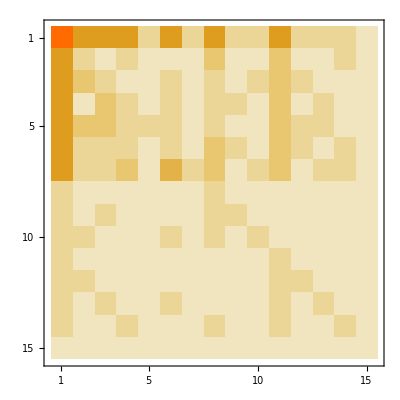

```mathematica
MatrixPlot[zet4.Inverse[fullToGen4 ]]
```